# Electromagnetic Fields in One Mathematica Notebook

## Unpublished Draft © 2022 Yifan Yu yifan.yu@aalto.fi

If people do not believe that mathematics is simple, it is only because they do not realize how complicated life is.
- John von Neumann

## Introduction

The goal of this notebook is to make the study of electromagnetic fields as visual and interactive as possible. I will assume that you already know something about this subject, or have a good textbook on your side, so that I can be terse with words and put more effort into the actual code and illustrations. I will do a lot of plots and use Manipulate and Animate whenever I deem necessary. So, please:

1. Run each cell yourself and see the results
2. Change some parameters or variables, re-run the cell, and see the effects
3. Interact with the interactive plots made possible with Manipulate 
4. Click the little play button to view the animations made possible with Animate

In addition, I will also adopt a Q&A style akin to the wonderful The Little Schemer.

Bon Appétit!

```mathematica
Remove["Global`*"]//Quiet
Symbolize[A]
Symbolize[Subscript[V, _]]
Symbolize[Ṽ]
Symbolize[OverTilde[Subscript[V, _]]]
Symbolize[J̃]
```

## Waves and Phasors

## The Basics

### Waves and Space Dependence

Welcome, I’m the imaginary teacher, I’m in black text.

Hi, I’m the imaginary student, I’m in gray text.

Good to have you here. We begin by studying waves. First, run the next cell (click the cell, then Shift+Enter) to set up some global Assumptions first.

```mathematica
$Assumptions={ϕ∈Reals,ω∈Reals,t∈Reals}
```

{ϕ∈ℝ,ω∈ℝ,t∈ℝ}

Now, play with the plot of the three functions , ,  below, what are the effects of changing ,ω and ϕ ?

```mathematica
Manipulate[Plot[{A Cos[ω t-ϕ],A Cos[ω t],A Cos[ω t+ϕ]},{t,-2,8},PlotLegends->Automatic],{A,1,5},{ω,1,5},{{ϕ,π/4},0,π}]
```

Easy peasy!  is the amplitude, and , we know that increasing  increases the frequency.  represents a phase shift, if  and you have , then the waveform is shifted to the left, and vice versa.

Do these waves have space (spatial?) variables?

No, it only has one time variable, . I guess it’s suitable for representing things like voltage or current in a circuit.

Can you think of some waves that have one space variables?

Well, if you have only one space variable (i.e. one-dimensional wave),  you could think of the displacement of a string when you play the guitar. The displacement varies with time as well as the location along the string. That location is the only space variable.

I noticed that you call this wave one-dimensional even though the guitar string clearly vibrates into a second dimension?

Yeah, I guess it’s because there is only one space variable, so it would be neat to call the wave one-dimensional. But I guess you have a point. I like to think of the dimension when the wave is not “vibrating” — a string is just a one-dimensional line.

Fair enough. What about waves that have two or three space variables?

For two-dimensional waves, you could think of ripples on a pond since the pond surface is two-dimensional. For three-dimensional waves, how about electromagnetic waves that propagate through space, which is three-dimensional?

Nice, I see you noticed that this course is about electromagnetic waves. But before we get ahead of ourselves, let’s step back and start with waves without space variables, i.e. things like . I assume you already know about phasors. How would you convert  into a phasor form ?

### Phasors

By the way, I quite like that you use the overhead tilde ~ to represent phasors. Many people aren’t that meticulous when it comes to notations.

Compliment taken. Now answer the question.

Alright. To convert an instantaneous function  into a phasor, it’s simply  — that time dependency  bit is dropped.

I glad that you noticed the time dependency is dropped. I guess one could call the phasor a time-invariant entity (and that’s perhaps the whole point!) Now, how do you convert the phasor back into an instantaneous function?

We multiple by  and take the real part, as in .

That’s right. You can check this yourself:

```mathematica
Refine[Re[ComplexExpand[2 ⅇ^(ⅉ ϕ)ⅇ^(ⅉ ω t)]]]
```

2 Cos[ϕ+t ω]

Why do you need Refine and ComplexExpand?

I guess that’s just how Mathematica works — it can be quite smart but sometimes you just need to help it a bit. Now, ready for a quiz?

Sure.

Convert the instantaneous function   into a phasor.

I guess you need to convert it to cosine first. If we didn’t do so, since , it would just vanish when you convert the phasor back by taking the real part! So we should use the property :

```mathematica
Sin[ω t+ϕ]==Cos[π/2-ω t - ϕ]&&Cos[π/2-ω t - ϕ]==Cos[ω t+ϕ-π/2]
```

True

So the phasor should just be :

```mathematica
Refine[Re[ComplexExpand[Subscript[V, 0] ⅇ^(ⅉ (ϕ-π/2))ⅇ^(ⅉ ω t)]],Subscript[V, 0]∈Reals]
```

V_0 Sin[ϕ+t ω]

Very good! It’s perhaps worth remembering this result, that the phasor of   is , if  is 0, then you know the phasor of   is . Now, the phasor can be very handy for many reasons. One important reason — and this is what I want you to show, is that taking the derivative of the instantaneous function against time is equivalent to multiplying its phasor by , while doing integration of the instantaneous function against time is equivalent to dividing its phasor by . In other words, , and .

I guess we could work backwards, i.e. start with a phasor, then convert it to the  instantaneous function after multiplying or dividing by :

```mathematica
Refine[Re[ComplexExpand[ⅉ ω Subscript[V, 0] ⅇ^(ⅉ (ϕ-π/2))ⅇ^(ⅉ ω t)]],Subscript[V, 0]∈Reals]
```

V_0 ω Cos[ϕ+t ω]

```mathematica
Refine[Re[ComplexExpand[(Subscript[V, 0] ⅇ^(ⅉ (ϕ-π/2)))/(ⅉ ω)ⅇ^(ⅉ ω t)]],Subscript[V, 0]∈Reals]
```

-V_0 Cos[ϕ+t ω] Re[1/ω]+V_0 Im[1/ω] Sin[ϕ+t ω]

```mathematica
Refine[Re[ 1/ω],ω∈Reals]
```

Re[1/ω]

```mathematica
Refine[Re[ 1/x],x∈Reals]
```

Re[1/x]

```mathematica
Assuming[x∈Reals,Refine[Re[ 1/x]]]
```

Re[1/x]

I don’t think that constitutes any sort of mathematical proof!

But you said to “show”, not to “proof”!

Fine, I’ll let you pass.

### Spatial Waves

Now it’s time to introduce some space variables!

Finally!

First, let’s do one-dimensional waves (one space variable). Given a general time-dependent function , how would you write the general form when one space variable  is introduced?

I guess you could simply feed  to cosine, as in ?

Almost there. Let’s just add a multiplier  to , you get . Now, we already know the effects of , , and , but what about ?

I guess we need to plot it and use Manipulate to see its effects.

How would you plot this function?

First of all, it’s a function of two real variables,  and . The output  is also real. You could say it’s a mapping from  to .

How do we normally think of a function that maps  to ?

Oh, I know, it’s a two dimensional scalar field!

```mathematica
Manipulate[DensityPlot[2Cos[2t-β x+π/2],{t,0,10},{x,0,10},Frame->False,Axes->True,AxesLabel->Automatic],{{β,5},1,10}]
```

As you can see, a larger  results in...

Can you think of another way to plot it?

I guess you could also visualize  as some kind of surface, such that the output  represents the “altitude” above the plane .

```mathematica
Manipulate[Plot3D[2Cos[2t-β x+π/2],{t,0,10},{x,0,10},AxesLabel->Automatic],{{β,5},1,10}]
```

Well, it’s interesting to see the two ways of plotting  you came up with both treat time  as a space variable. I guess one could think of the wave along the  axis at a given time by holding  constant and “slice through” the surface at a right angle. Moving the slice back-and-forth along  allows the wave to “travel”. On the other hand, you can try to simply treat  as time itself by using Animate.

Right, let me give it a shot.

```mathematica
Animate[Plot[2Cos[π t+ x+π/4],{x,-2,10},AxesLabel->Automatic],{t,0,5},AnimationRunning->False]
```

Aha, we got a wave traveling in the  direction! At , the phase shift is . Also,  means . In addition,   as given.

Good. But do you remember your original task? You were supposed to study how  affects the behavior of the wave.

Thanks for reminding me. Well, I’m already using Animate to control , I wonder if I could use Manipulate to control ?

```mathematica
Manipulate[Animate[Plot[2Cos[π t+β x+π/4],{x,-2,10},AxesLabel->Automatic],{t,0,5},AnimationRunning->False],{{β,1},-10,10}]
```

Mathematica is pretty neat. Now I can see that the sign of  controls the direction of travel: when it’s positive, the wave travels in the  direction; when it’s negative, the wave travels in the  direction. We can also see that as  gets larger, the wavelength decreases but the wave also travels a bit slower.

Good observations. Now, here is another small quiz: convert  into a phasor.

I’m familiar with the drill already. It’s just .  To convert the phasor back to its instantaneous counterpart, we multiply it with .  Here, .

```mathematica
Animate[Plot[Re[2 ⅇ^(ⅉ(-2x+π/4))ⅇ^(ⅉ π t)],{x,-2,10},AxesLabel->Automatic],{t,0,5},AnimationRunning->False]
```

I noticed that you didn’t use Refine and ComplexExpand this time.

Right, Mathematica seems to know what to do when plotting. I guess it uses numerical values for plotting so we are not doing symbolic computations.

Very good. Now I want you to play with the amplitude  a bit. So far, it has been a constant. What if it’s a value that changes with time? In electromagnetics, we are especially interested in changes of the form , for example:

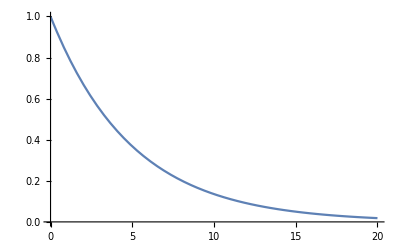

```mathematica
Plot[ⅇ^(-0.2 x),{x,0,20}]
```

represents exponential decay, I can see why it’s interesting since many things in nature decay exponentially.

Absolutely. How would a traveling wave with exponential decay look like?

I guess I could add  as a multiplier to the previous wave phasor , from which we get , and animate the instantaneous function.

```mathematica
Animate[Plot[Re[2 ⅇ^(-0.2x)ⅇ^(ⅉ(-2x+π/4))ⅇ^(ⅉ π t)],{x,0,10},AxesLabel->Automatic,PlotRange->{-2.5,2.5}],{t,0,5},AnimationRunning->False]
```

The decay is rather obvious here.

Indeed. We call the multiplier  the attenuation factor and  the attenuation constant. This occurs when the medium is lossy.

Like water?

Yes. We have much more to say about mediums later. For now, let’s still focus on waves. Another thing I would like to mention is that many waves are linear, which means that two waves can pass right through each other and the total wave is just the sum of both. Electromagnetic waves are linear.

You mean electromagnetic waves can be superpositioned like other “linear things”?

Exactly. Try to superpositioned two waves traveling in opposite directions and see what happens.

Ok, I’ll reuse the wave I’ve been plotting,  . Since  determines the direction of travel, the opposite wave would just be . To sum them up, I get :

```mathematica
Animate[Plot[Re[(2 ⅇ^(ⅉ(-2x+π/4))+2 ⅇ^(ⅉ(2x+π/4)))ⅇ^(ⅉ π t)],{x,0,10},AxesLabel->Automatic,PlotRange->{-5,5}],{t,0,5},AnimationRunning->False]
```

Interesting, I seem to get a wave that has the same wavelength but twice the amplitude, and it doesn’t seem to travel at all.

No, it doesn’t travel anywhere. This is what we call a standing wave. It occurs when a wave gets reflected at the interface between two mediums and the reflected wave is superpositioned onto the incident wave.

```mathematica
(* Animate[Plot[Re[(2 ⅇ^(0.2x)ⅇ^(ⅉ(-2x+π/4))+2 ⅇ^(0.1x)ⅇ^(ⅉ(2x+π/4)))ⅇ^(ⅉ π t)],{x,-10,0},AxesLabel->Automatic,PlotRange->{-5,5}],{t,0,5},AnimationRunning->False]*)
```

TODO: from now on, plot x < 0

Note that we are using ListAnimate to generate an animation frame by frame beforehand since Animate will run too slowly if there is lots of computation to do for each frame. This makes the animation smoother, but it will take a lot longer to run.

```mathematica
ListAnimate[Map[Plot3D[Re[2 ⅇ^(ⅉ(-2x-2y π/4))ⅇ^(ⅉ π #)],{x,-5,5},{y,-5,5},AxesLabel->Automatic]&,Range[0,5]],AnimationRunning->False]
```

```mathematica
Animate[SliceDensityPlot3D[Re[2 ⅇ^(ⅉ(-2x-2y-2z+π/4))ⅇ^(ⅉ π t)],"ZStackedPlanes",{x,-2,2},{y,-2,2},{z,-2,2}],{t,0,5},AnimationRunning->False]
```

What else can be said about these one-dimensional waves?

Let’s assume y(x,t) = A cos [(2π t)/T-(2π x)/λ+ϕ]. Since (2π)/T=2π f=ω, let (2π)/λ=β, this is just y(x,t)=A Cos[ω t-β x+ϕ].

```mathematica
Manipulate[Plot3D[2Cos[(2π t)/T-(2π x)/λ+π/2],{x,0,10},{t,0,10},AxesLabel->Automatic],{{T,5},1,100,1},{{λ,5},1,100,1}]
```

```mathematica
Animate[Plot[2Cos[(2π t)/5-(2π x)/5+π/2],{x,0,10},AxesLabel->Automatic],{t,0,10}]
```

```mathematica
Plot3D[2Cos[(2π t)/5-(2π x)/5+π/2],{x,0,10},{t,0,10},AxesLabel->Automatic]
```

-Graphics3D-

Given a wave, how do we know how fast it travels?

Phase velocity
Compact form P.41
Role of reference phase
Lossy medium
Complex numbers
2D & 3D waves, the k vector
1D wave with vector values

```mathematica
Animate[VectorPlot[{x+a,-y+a},{x,-3,3},{y,-3,3}],{a,1,5},AnimationRunning->False]
```

## Vector Analysis

## Medium

What kind of mediums do we usually talk about?

## Electrostatics

## Magnetostatics

## Maxwell’s Equations for Time-Varying Fields

What are the names of the Maxwell’s equations, and what do they say, in human language?

Well,
1. Gauss’s law says that; 
2. Gauss’s law for magnetism says that;
3. Faraday’s law says that;
4. Ampère’s law says that;

Good. Now, write down the differential form of each of these equations.

That should be simple enough.

## Plane-waves Propagation

What are the Maxwell’s equations in the phasor domain?

Derive the wave equation

propagation constant

intrinsic impedance

phase velocity

What is a plane wave? https://reference.wolfram.com/language/ref/SliceVectorPlot3D.html

How is the conduction current  (try to achieve \vb) related to conductivity ?

```mathematica
SliceVectorPlot3D[{y,-x,z},"ZStackedPlanes",{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

## Wave Reflection and Transmission